```mathematica
Quit
```

```mathematica
If[True,
<<TenTenData`,
<<MBokeh`
]
If[True,  MBokehStartWebDriver["Headless"->False]];
```

WebDriver-Chrome {590, 710}

```mathematica
MBokehStartWebDriver["Headless"->False];
(*MBokehStartWebDriver["Headless"->True];*)
```

```mathematica
$ContextPath
```

{ExternalEvaluateWebDriver`,ExternalEvaluate`,ZeroMQLink`,ZeroMQLink`HostParser`,ZeroMQLink`SocketOptions`,ZeroMQLink`Libraries`,MmaCloud`,MBokehCharts`,MExcel`,MBokehK`,MBokeh`,Dataset`,TypeSystem`,MClasses`,MClasses`Core`GenericClasses`,MClasses`Utils`Couch`,MClasses`Utils`Utils`,MClasses`Utils`MSync`,MClasses`Core`MPlusPlus`,JLink`,TenTenData`,TenTenData`Export`,TenTenData`TenTenAPI`,TenTenData`Environment`,DivergentColorMaps`,TenTenKLink`,Parallel`Developer`,Parallel`Debug`Perfmon`,Parallel`Debug`,TenTenFormat`,XMLParser`,Association`,HierarchicalClustering`,StatisticalPlots`,ErrorBarPlots`,Developer`,DocumentationSearch`,ResourceLocator`,WolframAlphaClient`,CloudPublishMenu`,SystemTools`,ExternalEvaluateLoader`,PacletManager`,System`,Global`}

### DisplayFunction

```mathematica
Quit
```

```mathematica
MBokehDisplayFunction
```

MBokehDisplayFunction

```mathematica
ExternalEvaluate[MBokeh`Private`$WebSession, "WindowSize"]
ExternalEvaluate[MBokeh`Private`$WebSessionHeadless, "WindowSize"]
```

{590,710}

StartExternalSession::invalidSpec: The session specification None is invalid.

$Failed

```mathematica
show[Graphics[{Pink,Rectangle[]}]]
```

-Graphics-

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]//show
```

-Graphics-

```mathematica
RegionPlot3D[x y z<1,{x,-5,5},{y,-5,5},{z,-5,5},PlotStyle->Directive[Yellow,Opacity[0.5]],Mesh->None]//show
```

-Graphics-

```mathematica
SphericalPlot3D[1+Sin[5θ]Sin[5ϕ]/5,{θ,0,Pi},{ϕ,0,2Pi},Mesh->None,RegionFunction->(#6>0.95&),PlotStyle->FaceForm[Orange,Yellow]]//show
```

-Graphics-

```mathematica
data=RandomVariate[NormalDistribution[RandomInteger[5],1],{8,50}];
BoxWhiskerChart[data,"Outliers",ChartStyle->56, PerformanceGoal->"Speed"]//show
```

-Graphics-

```mathematica
data=Table[RandomVariate[NormalDistribution[RandomInteger[5],1],100],{10}];
DistributionChart[data,ChartStyle->"SandyTerrain",PerformanceGoal->"Speed"]//show
```

-Graphics-

```mathematica
data=FinancialData["IBM","OHLCV",{{2009,5,1},{2010,4,30}}];
TradingChart[data,PerformanceGoal->"Speed"]//show
```

-Graphics-

```mathematica
ThermometerGauge[25,{0,100}]//show
```

-Graphics-

```mathematica
AngularGauge[{15,42,63,88},{0,100}]//show
```

-Graphics-

```mathematica
MBokehStopWebDriver[]
```

### decodejson

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
data="{'event_name':'pan','event_values':{'model_id':1,'x':10,'y':20,'sx':200,'sy':37}}"
```

{'event_name':'pan','event_values':{'model_id':1,'x':10,'y':20,'sx':200,'sy':37}}

```mathematica
ev=events.Event.decodejson[data]
```

Pan[<⋯>]

```mathematica
ev.tableform[]
```

_event_classes | 
event_name | pan
model | None
_model_id | 1
sx | 200
sy | 37
x | 10
y | 20
delta_x | None
delta_y | None
direction | None

### TextInput

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
textinput=TextInput["value"->"default", "title"->"Label:", "width"->100, "height"->8]
show[widgetbox[textinput]]
```

TextInput[<⋯>]

-Graphics-

```mathematica
textinput.normalize
```

<|attributes→<|callback→Null,height→8,title→Label:,value→default,width→100|>,id→EID-275,type→TextInput|>

### Toggle Button

```mathematica
Quit
```

```mathematica
$Version
```

11.3.0 for Microsoft Windows (64-bit) (March 7, 2018)

```mathematica
mb=MBokeh`Private`$MasterBokehBag
```

Bag[<0>]

```mathematica
mb.reset[]
```

Internal`Bag[<0>]

```mathematica
toggle=ToggleWidget["label"->"foo1", "button_type"->"success"]
wbox=widgetbox[toggle]
```

Toggle[<⋯>]

```mathematica
toggle.references[]
```

ToggleWidgetClass

{Toggle[<⋯>]}

```mathematica
toggle.normalize[]
```

ToggleWidgetClass

<|attributes→<|button_type→success,callback→Null,icon→Null,label→foo1|>,id→EID-1,type→Toggle|>

```mathematica
show[wbox]
```

WidgetBoxClass

ToggleWidgetClass

C:\Users\ulises.cervantes\AppData\Local\Temp\mbokeh.html

```mathematica
wbox.rawjson[]
```

{
	"attributes":{
		"children":[
			{
				"id":"EID-1",
				"type":"Toggle"
			}
		]
	},
	"id":"EID-2",
	"type":"WidgetBox"
}

```mathematica
wbox.serializeJSON[]
```

[
	{
		"attributes":{
			"button_type":"success",
			"callback":null,
			"icon":null,
			"label":"foo1"
		},
		"id":"EID-1",
		"type":"Toggle"
	},
	{
		"attributes":{
			"children":[
				{"id":"EID-1","type":"Toggle"}
			]
		},
		"id":"EID-2",
		"type":"WidgetBox"
	}
]

```mathematica
mb.all[]
```

{Toggle[<⋯>],WidgetBox[<⋯>]}

```mathematica
wbox.inspect["WidgetBox"]
```

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$20106,#1[type]===FE`MBokeh`Private`type$$438&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$20106,#1[type]===FE`MBokeh`Private`type$$167&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$20106,#1[type]===FE`MBokeh`Private`type$$17&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$20106,#1[type]===FE`MBokeh`Private`type$$17&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$20106,#1[type]===FE`MBokeh`Private`type$$486&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

### Dropdown Menu

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
menu={{"Item 1","item_1"},{"Item 2","item_2"},None,{"Item 3","item_3"}};
dropdown=DropdownWidget["label"->"Dropdown button","button_type"->"warning","menu"->menu];
show[widgetbox[dropdown]]
```

-Graphics-

### Tab Panes

```mathematica
Quit
```

```mathematica
$Version
```

11.3.0 for Microsoft Windows (64-bit) (March 7, 2018)

```mathematica
p1=Figure["plot_width"->500,"plot_height"->500];
p1.circle[{1,2,3,4,5},{6,7,2,4,5},"size"->20,"color"->"navy","alpha"->0.5];
tab1=PanelWidget["child"->p1,"title"->"Circle"];
p2=Figure["plot_width"->500,"plot_height"->500];
p2.line[{1,2,3,4,5},{6,7,2,4,5},"Line_width"->3,"color"->"navy","alpha"->0.5];
tab2=PanelWidget["child"->p2,"title"->"line"];

tabs=Tabs["tabs"->{tab1,tab2}];
show[tabs]
```

-Graphics-

### Multiselect

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
multiselect=MultiSelect["title"->"Option:","value"->{"foo","quux"},"options"->{{"foo","Foo"},{"bar","BAR"},{"baz","bAz"},{"quux","quux"}}]

show[widgetbox[multiselect]]
```

MultiSelect[<⋯>]

-Graphics-

### JavaScript Callback

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
x=Table[x*0.005 , {x,0,200,1}];
y=x;

source=ColumnDataSource["data"-><|"x"->x,"y"->y|>];

plot=figure["plot_width"->400,"plot_height"->400];
plot.line["x","y","source"->source,"line_width"->3,"line_alpha"->0.6];

callback1=CustomJS["args"-><|"source"->source|>,"code"->"
    var data = source.data
    var f = cb_obj.value
    var x = data['x']
    var y = data['y']
    for (var i = 0; i < x.length; i++) {
        y[i] = Math.pow(x[i], f)
    }
    source.change.emit()
"];

slider=SliderWidget["start"->0.1,"end"->4,"value"->1,"step"->.1,"title"->"power"];
slider.jsonchange["value",callback1]

layout1=column[slider,plot];
show[layout1]
```

-Graphics-

### CustomJS for Selections

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

#### Ex 1

```mathematica
x=RandomReal[{0,1},500];
y=RandomReal[{0,1},500];

s1=ColumnDataSource["data"-><|"x"->x,"y"->y|>];
p1=figure["plot_width"->400,"plot_height"->400,"tools"->{"LassoSelect","Reset"},"title"->"Select Here"];
p1.scatter["x","y","source"->s1,"alpha"->0.6, "size"->15, "line_alpha"->0];

s2=ColumnDataSource["data"-><|"x"->{1},"y"->{1}|>];
p2=figure["plot_width"->400,"plot_height"->400,"x_range"->{0,1},"y_range"->{0,1},"tools"->"","title"->"Watch Here"];
p2.scatter["x","y","source"->s2,"alpha"->0.6];

s1."callback"=CustomJS["args"-><|"s2"->s2|>,"code"->"
        var inds = cb_obj.selected.indices;
        var d1 = cb_obj.data;
        var d2 = s2.data;
        d2['x'] = []
        d2['y'] = []
        for (var i = 0; i < inds.length; i++) {
            d2['x'].push(d1['x'][inds[i]])
            d2['y'].push(d1['y'][inds[i]])
        }
        s2.change.emit();
    "];

layout1=row[p1,p2];
show[layout1]
```

-Graphics-

#### Ex 2

```mathematica
x=RandomReal[{0,1},{500}];
y=RandomReal[{0,1},{500}];
color=Table["navy",{500}];

s=ColumnDataSource["data"-><|"x"->x,"y"->y,"color"->color|>];
p=figure["plot_width"->400,"plot_height"->400,"tools"->{"LassoSelect", "Reset"},"title"->"Select Here", "toolbar_location"->"right"];
p.scatter["x","y","color"->"color","size"->8,"source"->s,"alpha"->0.4];

s2=ColumnDataSource["data"-><|"x"->{0,1},"ym"->{0.5,0.5}|>];
p.line["x"->"x","y"->"ym","color"->"orange","line_width"->5,"alpha"->0.6,"source"->s2];

s."callback"=CustomJS["args"-><|"s2"->s2|>,"code"->"
        var inds = cb_obj.selected.indices;
        var d = cb_obj.data;
        var ym = 0

        if (inds.length == 0)
            return;

        for (var i = 0; i < d['color'].length; i++) {
            d['color'][i] = \"navy\"
        }
        for (var i = 0; i < inds.length; i++) {
            d['color'][inds[i]] = \"firebrick\"
            ym += d['y'][inds[i]]
        }

        ym /= inds.length
        s2.data['ym'] = [ym, ym]

        cb_obj.change.emit();
        s2.change.emit();
    "];

show[p]
```

-Graphics-

### CustomJS for Hover

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
x={2,3,5,6,8,7};
y={6,4,3,8,7,5};
links=<|"0"->{1,2},"1"->{0,3,4},"2"->{0,5},"3"->{1,4},"4"->{1,3},"5"->{2,3,4}|>;
slinks = StringReplace[ExportString[links,"RawJSON", "Compact"->0],"\""->""];

p=figure["plot_width"->400,"plot_height"->400,"tools"->{},"toolbar_location"->None,"title"->"Hover over points"];

source=ColumnDataSource[<|"x0"->{},"y0"->{},"x1"->{},"y1"->{}|>];
sr=p.segment["x0"->"x0","y0"->"y0","x1"->"x1","y1"->"y1","color"->"olive","alpha"->0.6,"line_width"->3,"source"->source];
cr=p.circle[x,y,"color"->"olive","size"->30,"alpha"->0.4,"hover_color"->"olive","hover_alpha"->1.0];

(* Add a hover tool,that sets the link data for a hovered circle *)
code=StringTemplate["
var links = ``;
var data = {'x0': [], 'y0': [], 'x1': [], 'y1': []};
var cdata = circle.data;
var indices = cb_data.index['1d'].indices;
for (var i = 0; i < indices.length; i++) {
    var ind0 = indices[i]
    for (var j = 0; j < links[ind0].length; j++) {
        var ind1 = links[ind0][j];
        data['x0'].push(cdata.x[ind0]);
        data['y0'].push(cdata.y[ind0]);
        data['x1'].push(cdata.x[ind1]);
        data['y1'].push(cdata.y[ind1]);
    }
}
segment.data = data;
"][slinks];

callback1=CustomJS["args"-><|"circle"->cr."data_source","segment"->sr."data_source"|>,"code"->code];
p.addtools[HoverTool["tooltips"->None,"callback"->callback1,"renderers"->{cr}]]

show[p]
```

-Graphics-

### CustomJS for Tools

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
source=ColumnDataSource["data"-><|"x"->{},"y"->{},"width"->{},"height"->{}|>];
callback1=CustomJS["args"-><|"source"->source|>,"code"->"
        // get data source from Callback args
        var data = source.data;

        /// get BoxSelectTool dimensions from cb_data parameter of Callback
        var geometry = cb_data['geometry'];

        /// calculate Rect attributes
        var width = geometry['x1'] - geometry['x0'];
        var height = geometry['y1'] - geometry['y0'];
        var x = geometry['x0'] + width/2;
        var y = geometry['y0'] + height/2;

        /// update data source with new Rect attributes
        data['x'].push(x);
        data['y'].push(y);
        data['width'].push(width);
        data['height'].push(height);

        // emit update of data source
        source.change.emit();
    "];
boxselect=BoxSelectTool["callback"->callback1];

(* TODO: Fix "tools" option *)
p=figure["plot_width"->400,"plot_height"->400,"tools"->{"Save"},"title"->"Select Below","x_range"->Range1d["start"->0.0,"end"->1.0],"y_range"->Range1d["start"->0.0,"end"->1.0], "toolbar_location"->"right"];

rect1=Rect["x"->"x","y"->"y","width"->"width","height"->"height","fill_alpha"->0.3,"fill_color"->"#009933"];

p.addtools[boxselect];

p.addglyph[source,rect1,"selection_glyph"->rect1,"nonselection_glyph"->rect1];
show[p]
```

-Graphics-

### CustomJS for Range Updates (Not working yet )

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
NN=400;

x=RandomReal[{0,100},{NN}];
y=RandomReal[{0,100},{NN}];
radii=RandomReal[{0,1.5},{NN}];
colors=RGBToHex/@(ColorData["TemperatureMap"]/@RandomReal[{0,0.8},{NN}]);

source=ColumnDataSource[<|"x"->{},"y"->{},"width"->{},"height"->{}|>];

jscode="
    var data = source.data;
    var start = cb_obj.start;
    var end = cb_obj.end;
    data[``] = [start + (end - start) / 2];
    data[``] = [end - start];
    source.change.emit();
";
```

```mathematica
p1=figure["title"->"Pan and Zoom Here","x_range"->{0,100},"y_range"->{0,100},"tools"->{"BoxZoom","WheelZoom","Pan","Reset"},"plot_width"->400,"plot_height"->400];
p1.circle[x,y,"radius"->radii,"fill_color"->colors,"fill_alpha"->0.6,"line_color"->None];
```

```mathematica
p1."x_range"."callback"=CustomJS["args"-><|"source"->source|>,"code"->StringTemplate[jscode]["x","width"]];
p1."y_range"."callback"=CustomJS["args"-><|"source"->source|>,"code"->StringTemplate[jscode]["y","height"]];
```

```mathematica
p2=figure["title"->"See Zoom Window Here","x_range"->{0,100},"y_range"->{0,100},"tools"->{},"plot_width"->400,"plot_height"->400];
p2.circle[x,y,"radius"->radii,"fill_color"->colors,"fill_alpha"->0.6,"line_color"->None];
rect=Rect["x"->"x","y"->"y","width"->"width","height"->"height","fill_alpha"->0.1,"line_color"->"black","fill_color"->"black"];
p2.addglyph[source,rect];
```

```mathematica
layout1=row[p1,p2]

show[layout1]
```

Row[<⋯>]

### GMap

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
mapoptions=GMapOptions["lat"->40.74598,"lng"->-73.9623,"map_type"->"roadmap","zoom"->13, "logo"->None];

p=gmap[mapoptions, "width"->600, "x_axis_label"->"Hi"];

nn=80;
lat=RandomReal[{40.70, 40.80},{nn}];
lon=RandomReal[{-74, -73.9},{nn}];
source = ColumnDataSource[<|"lat"->lat, "lon"->lon|>];
p.triangle["x"->"lon", "y"->"lat", "size"->20, "fill_color"->"orange", "fill_alpha"->0.6, "source"->source];

nn=50;
lat=RandomReal[{40.70, 40.80},{nn}];
lon=RandomReal[{-74, -73.9},{nn}];
source = ColumnDataSource[<|"lat"->lat, "lon"->lon|>];
p.circle["x"->"lon", "y"->"lat", "size"->20, "fill_color"->"blue", "fill_alpha"->0.6, "source"->source];
show[p]
```

-Graphics-

### Geo Data

```mathematica
Quit
```

```mathematica
gtype={"CARTODBPOSITRON", "CARTODBPOSITRON_RETINA", "STAMEN_TERRAIN", "STAMEN_TERRAIN_RETINA", "STAMEN_TONER", "STAMEN_TONER_BACKGROUND", "STAMEN_TONER_LABELS"};

nn=3;
p=figure["x_range"->{-2000000,6000000},"y_range"->{-1000000,7000000},"x_axis_type"->"mercator","y_axis_type"->"mercator"];
p.addtile[TileProviders[gtype[[nn]]]];

show[p]
```

-Graphics-

### OpenURL

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
p=figure["plot_width"->400,"plot_height"->400,"tools"->"tap,reset","title"->"Click the Dots"];

source=ColumnDataSource["data"-><|"x"->{1,2,3,4,5},"y"->{2,5,8,2,7},"color"->{"navy","orange","olive","firebrick","gold"}|>];

p.circle["x","y","color"->"color","size"->20,"source"->source];

(* use the "color" column of the CDS to complete the URL
# e.g.if the glyph at index 10 is selected,then@color
# will be replaced with source.data['color'][10]*)
url="http://www.colors.commutercreative.com/@color/";
taptool=p.select["type"->TapToolClass,None];
taptool."callback"=OpenURL["url"->url];

show[p]
```

-Graphics-

### CustomJS on Events ( Not working yet )

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
DisplayEvent[div_,attributes_:{},style_:"float:left;clear:left;font_size=10pt"] :=
CustomJS["args"-><|"div"->div|>,"code"->StringTemplate["
        var attrs = `a`; var args = [];
        for (var i = 0; i<attrs.length; i++) {
            args.push(attrs[i] + '=' + Number(cb_obj[attrs[i]]).toFixed(2));
        }
        var line = '<span style=`b`><b>' + cb_obj.event_name + '</b>(' + args.join(',') + ')</span>\\n';
        var text = div.text.concat(line);
        var lines = text.split('\\n')
        if (lines.length > 35)
            lines.shift();
        div.text = lines.join('\\n');
    "][<|"a"->attributes,"b"->style|>]]
```

```mathematica
NN=40;
x=RandomReal[{0,100},{NN}];
y=RandomReal[{0,100},{NN}];
radii=RandomReal[{0,1.5},{NN}];
colors=RGBToHex/@(ColorData["TemperatureMap"]/@RandomReal[{0,0.8},{NN}]);
```

```mathematica
p=figure["tools"->{"Pan","WheelZoom","ZoomIn","ZoomOut","Reset"}];
p.circle[x,y,"radius"->RandomReal[{0,1.5},{NN}],"fill_color"->colors,"fill_alpha"->0.6,"line_color"->None];
```

```mathematica
div=DivWidget["width"->1000];
button=ButtonWidget["label"->"Button","button_type"->"success"];
layout1=column[button,row[p,div]];
```

```mathematica
(* Events with no attributes *)
button.jsonevent[events.ButtonClick,DisplayEvent[div]] (* # Button click *)
p.jsonevent[events.LODStart,DisplayEvent[div]] (* Start of LOD display *)
p.jsonevent[events.LODEnd,DisplayEvent[div]] (* End of LOD display *)
```

```mathematica
(*Events with attributes *)
pointattributes={"x","y","sx","sy"} ;(* Point events *)
wheelattributes=Append[pointattributes,"delta"]; (* Mouse wheel event *)
panattributes=Join[pointattributes, {"delta_x","delta_y"}]; (* Pan event *)
pinchattributes=Append[pointattributes, "scale"]; (* Pinch event *)
```

```mathematica
pointevents={events.TapEvent,events.DoubleTap,events.Press,events.MouseMove,events.MouseEnter,events.MouseLeave,events.PanStart,events.PanEnd,events.PinchStart,events.PinchEnd};
```

```mathematica
Scan[(
p.jsonevent[#,DisplayEvent[div,pointattributes]]
)&, pointevents]
```

```mathematica
p.jsonevent[events.MouseWheel,DisplayEvent[div,wheelattributes]];
p.jsonevent[events.Pan,DisplayEvent[div,panattributes]];
p.jsonevent[events.Pinch,DisplayEvent[div,pinchattributes]];
```

```mathematica
p.inspect[]
```

```mathematica
show[layout1]
```

### Div

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
div=DivWidget["text"->"Your <a href='https://en.wikipedia.org/wiki/HTML'>HTML</a>-supported text is initialized with the <b>text</b> argument.  The
remaining div arguments are <b>width</b> and <b>height</b>. For this example, those values
are <i>200</i> and <i>100</i> respectively.","width"->200,"height"->100];
show[widgetbox[div]]
```

-Graphics-

### Linked Panning

```mathematica
Quit
```

```mathematica
$Version
```

10.4.0 for Microsoft Windows (64-bit) (February 26, 2016)

```mathematica
x=Range[11];
y0=x;
y1 = (10-#)& /@ x;
y2=(Abs[#-5])& /@ x;

(* create a new plot *)
s1=Figure["plot_width"->250,"plot_height"->250,"title"->None, "toolbar_location"->None];
AbsoluteTiming[s1.circle[x,y0,"size"->10,"color"->"navy","alpha"->0.5];]
(* create a new plot and share both ranges *)
s2=Figure["plot_width"->250,"plot_height"->250,"x_range"->s1."x_range","y_range"->s1."y_range","title"->None, "toolbar_location"->None];
s2.triangle[x,y1,"size"->10,"color"->"firebrick","alpha"->0.5];
(* create a new plot and share only one range *)
s3=Figure["plot_width"->250,"plot_height"->250,"x_range"->s1."x_range","title"->None, "toolbar_location"->None];
s3.square[x,y2,"size"->10,"color"->"olive","alpha"->0.5];

p=gridplot[{{s1,s2,s3}}, "toolbar_location"->None];

show[p]
```

{0.182928,Null}

-Graphics-

### Linked Brushing

```mathematica
Quit
```

```mathematica
x=Range[-20,21];
y0=Abs[#]& /@  x;
y1=#^2& /@  x;

(* create a column data source for the plots to share *)
source=ColumnDataSource["data"-><|"x"->x,"y0"->y0,"y1"->y1|>];
tools={"BoxSelect", "LassoSelect", "Help"};

(*create a new plot and add a renderer *)
left=Figure["tools"->tools,"plot_width"->300,"plot_height"->300,"title"->None];
left.circle["x","y0","source"->source];

(*create another new plot and add a renderer *)
right=Figure["tools"->tools,"plot_width"->300,"plot_height"->300,"title"->None];
right.circle["x","y1","source"->source];

p=gridplot[{{left,right}}];
show[p]
```

-Graphics-

### Widgets

```mathematica
Quit
```

```mathematica
button1=ButtonWidget["label"->"Button_1"];
button2=ButtonWidget["label"->"Button_2"];
slider = SliderWidget["start"->0, "end"->10, "value"->1, "step"->.1, "title"->"Slider"];
select1 = SelectWidget["title"->"Option:","value"->"foo","options"->{"foo","bar","baz","quux"}];
buttongroup=RadioButtonGroup["labels"->{"Option 1","Option 2","Option 3"},"active"->0];
button1.jsonevent[events.ButtonClick,CustomJS["code"->"console.log('JS:Click')"]]
wbox = widgetbox[{button1, slider, buttongroup,select1,button2}, "width"->300];
show[wbox]
```

-Graphics-

```mathematica
wbox.inspect[]
```

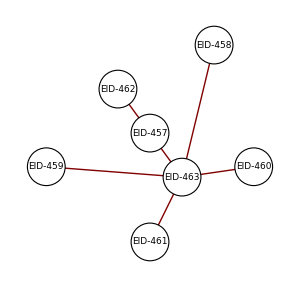

```mathematica
BokehGraph[wbox,ImageSize->300]
```

```mathematica
{wbox.inspect[],InspectAttributes["layout_widgets.html"]}
```

```mathematica
WidgetBox["children"->{button_1}]
```

WidgetBox[<⋯>]

```mathematica
rowbox=row[{button1,slider}, "width"->600]
```

Row[<⋯>]

```mathematica
rowbox.inspect[]
```

```mathematica
show[rowbox]
```

```mathematica
columnbox=column[{button2,select}, "width"->600]
```

Column[<⋯>]

```mathematica
columnbox.inspect[]
```

```mathematica
show[columnbox]
```

```mathematica
layoutbox=layout[{{button1,slider},{button2, select}}]
```

Column[<⋯>]

```mathematica
layoutbox.references[]
```

{Button[<⋯>],Button[<⋯>],Column[<⋯>],CustomJS[<⋯>],Row[<⋯>],Row[<⋯>],Select[<⋯>],Slider[<⋯>],WidgetBox[<⋯>],WidgetBox[<⋯>],WidgetBox[<⋯>],WidgetBox[<⋯>]}

```mathematica
show[layoutbox]
```

```mathematica
layoutbox.inspect[]
```

```mathematica
{layoutbox.inspect[],InspectAttributes["layout_widgets.html"]}
```

```mathematica
layoutbox=layout[{{button1,slider},{button2, select}, buttongroup}]
```

Column[<⋯>]

```mathematica
show[layoutbox]
```

```mathematica
Partition[{1,2,3},2]
```

{{1,2}}

```mathematica
Take
```

```mathematica
Take[{1,2,3,4,5,6}, -0]
```

{}

### gridplot

```mathematica
Quit
```

```mathematica
button1=ButtonWidget["label"->"Button_1"];
button1.jsonevent[events.ButtonClick,CustomJS["code"->"console.log('JS:Click')"]]

button2=ButtonWidget["label"->"Button_2"];
slider = SliderWidget["start"->0, "end"->10, "value"->1, "step"->.1, "title"->"Slider"];
select1 = SelectWidget["title"->"Option:","value"->"foo","options"->{"foo","bar","baz","quux"}];
buttongroup=RadioButtonGroup["labels"->{"Option 1","Option 2","Option 3"},"active"->0];

p1=Figure["plot_width"->400, "plot_height"->400];
p1.annularwedge["x"->{1,2,3},"y"->{1,2,3}, "inner_radius"->0.1, "outer_radius"->0.25, "start_angle"->0.4, "end_angle"->4.8, "color"->"green", "alpha"->0.6];
p2=Figure["plot_width"->400, "plot_height"->400];
p2.annulus["x"->{1,2,3},"y"->{1,2,3}, "inner_radius"->0.1, "outer_radius"->0.25, "color"->"orange", "alpha"->0.6];
p3=Figure["plot_width"->400, "plot_height"->400];
p3.arc["x"->{1,2,3},"y"->{1,2,3}, "radius"->0.1, "start_angle"->0.4, "end_angle"->4.8, "color"->"navy"];
p4=Figure["plot_width"->400, "plot_height"->400];
p4.ellipse[{1,2,3},{1,2,3},"width"->{0.2,0.3,0.1}, "height"->0.3,"angle"->Pi/3, "color"->"#CAB2D6"];
```

```mathematica
show[p1]
```

-Graphics-

```mathematica
gplot=gridplot[{p1,p2, p3},"ncols"->2, "toolbar_location"->"above", "merge_tools"->True, "plot_width"->200, "plot_height"->200]
```

Column[<⋯>]

```mathematica
show[gplot]
```

-Graphics-

```mathematica
gplot=row[{button1,p1, p2,Null, slider, p3}];
show[gplot]
```

Only LayoutDOM items can be inserted into a row.
Tried to insert: Null of type Null . MBokeh`Private`type[]

-Graphics-

```mathematica
gplot=gridplot[{button1,p1, p2,Null, slider, p3},"ncols"->2, "toolbar_location"->"below", "merge_tools"->True]
```

Column[<⋯>]

```mathematica
show[gplot]
```

-Graphics-

```mathematica
gplot=gridplot[{{button1,None,p1}, {p2},{None, slider, p3}},"toolbar_location"->"below", "merge_tools"->True]
```

$Failed

```mathematica
gplot=layout[{{p1},{p2,p3},{p4}}, "sizing_mode"->"stretch_both"]
```

Column[<⋯>]

```mathematica
show[gplot]//AbsoluteTiming
```

{8.7167,-Graphics-}

```mathematica
gplot.inspect[]
```

### Dataset

```mathematica
dataset=Dataset[<|
1-><|"a"->1,"b"->"x","c"->{1}|>,
"2001"-><|"a"->2,"b"->"y","c"->{2,3}|>,
"2002"-><|"a"->3,"b"->"z","c"->{3}|>,
"2003"-><|"a"->4,"b"->"x","c"->{4,5}|>,
5-><|"a"->5,"b"->"y","c"->{5,6,7}|>,
6-><|"a"->6,"b"->"z","c"->{}|>
|>]
```

| a | b | c
1 | 1 | x | { 1 }
2001 | 2 | y | { 2,3 }
2002 | 3 | z | { 3 }
2003 | 4 | x | { 4,5 }
5 | 5 | y | { 5,6,7 }
6 | 6 | z | {  }
3 levels | 6rows |  |  | Dataset[_Association]

```mathematica
dataset[5]
```

a | 5
b | y
c | { 5,6,7 }
2 levels | 3rows | Dataset[<|"a" -> _, "b" -> _, "c" -> _|>]

```mathematica
FullForm[dataset]
```

Dataset[Association[Rule[1,Association[Rule["a",1],Rule["b","x"],Rule["c",List[1]]]],Rule["2001",Association[Rule["a",2],Rule["b","y"],Rule["c",List[2,3]]]],Rule["2002",Association[Rule["a",3],Rule["b","z"],Rule["c",List[3]]]],Rule["2003",Association[Rule["a",4],Rule["b","x"],Rule["c",List[4,5]]]],Rule[5,Association[Rule["a",5],Rule["b","y"],Rule["c",List[5,6,7]]]],Rule[6,Association[Rule["a",6],Rule["b","z"],Rule["c",List[]]]]],TypeSystem`Assoc[TypeSystem`AnyType,TypeSystem`Struct[List["a","b","c"],List[TypeSystem`Atom[Integer],TypeSystem`Atom[TypeSystem`Enumeration["x","y","z"]],TypeSystem`Vector[TypeSystem`Atom[Integer],TypeSystem`AnyLength]]],6],Association[Rule["ID",31426416096216]]]

```mathematica
gb=GroupBy[dataset,"b"]
```

x | <|⋯_2|>
y | <|⋯_2|>
z | <|⋯_2|>
4 levels | 3rows | Dataset[Association[("x" | "y" | "z" -> _Association)..]]

```mathematica
Dimensions[gb]
```

{3}

```mathematica
Keys[gb][1]
```

x

```mathematica
gb[Keys[gb][1]]//Keys
```

{ 1,2003 }
1 level | 2elementsDataset[_List]

```mathematica
gb[Keys[gb][2]]
```

| a | b | c
2001 | 2 | y | { 2,3 }
5 | 5 | y | { 5,6,7 }
3 levels | 2rows |  |  | Dataset[_Association]

```mathematica
gb[Keys[gb][3]]
```

| a | b | c
2002 | 3 | z | { 3 }
6 | 6 | z | {  }
3 levels | 2rows |  |  | Dataset[_Association]

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
```

class | age | sex | survived
1st | 29 | female | True
1st | 1 | male | True
1st | 2 | female | False
1st | 30 | male | False
1st | 25 | female | False
1st | 48 | male | True
1st | 63 | female | True
1st | 39 | male | False
1st | 53 | female | True
1st | 71 | male | False
1st | 47 | male | False
1st | 18 | female | True
1st | 24 | female | True
1st | 26 | female | True
1st | 80 | male | True
1st | missing | male | False
⋮_1293 |  |  | 
2 levels | 1309rows |  |  | Dataset[{__Association}]

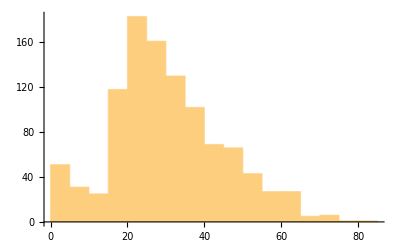

```mathematica
titanic[Histogram,"age"]
```

```mathematica
titanic[GroupBy[Key["class"]],Histogram[#,{0,80,4}]&,"age"]
```

1st | -Graphics-
2nd | -Graphics-
3rd | -Graphics-
1 level | 3elements | Dataset[Association[("1st" | "2nd" | "3rd" -> _Graphics)..]]

```mathematica
Dataset[RandomReal[{-10,10},{5,4}]]
```

-3.437 | 1.253 | 3.802 | -3.177
5.751 | 7.32 | 7.563 | -8.93
-0.1 | 7.479 | -9.127 | 2.396
-2.793 | 8.924 | -9.285 | -9.964
-5.667 | -5.783 | 7.594 | 2.125
2 levels | 5rows |  |  | Dataset[{__List}]

```mathematica
Dataset[AssociationThread[{1,2,3,4,5}->RandomReal[{-10,10},{5,4}]]]
```

1 | -6.105 | 8.103 | -4.664 | -8.152
2 | -5.538 | -2.152 | 2.384 | -1.941
3 | 2.598 | -2.905 | 4.705 | -3.711
4 | 8.961 | -3.122 | 6.357 | 8.24
5 | -1.237 | 7.84 | 1.582 | -1.589
2 levels | 5rows |  |  |  | Dataset[Association[(_Integer -> _List)..]]

```mathematica
ds1=Dataset[AssociationThread[{"A","B","C","D"}->#]& /@ RandomReal[{-10,10},{5,4}]]
```

A | B | C | D
7.58 | -8.783 | 8.175 | 6.115
-6.335 | 3.006 | -3.399 | -9.458
4.842 | -7.582 | 3.953 | -7.243
-9.201 | -5.931 | -7.394 | -8.594
5.009 | -1.162 | -9.229 | -2.396
2 levels | 5rows |  |  | Dataset[{__Association}]

```mathematica
ds1
```

A | B | C | D
7.58 | -8.783 | 8.175 | 6.115
-6.335 | 3.006 | -3.399 | -9.458
4.842 | -7.582 | 3.953 | -7.243
-9.201 | -5.931 | -7.394 | -8.594
5.009 | -1.162 | -9.229 | -2.396
2 levels | 5rows |  |  | Dataset[{__Association}]

```mathematica
ds=Dataset[AssociationThread[{1,2,3,4,5}->(AssociationThread[{"A","B","C","D"}->#]& /@ RandomReal[{-10,10},{5,4}])]]
```

| A | B | C | D
1 | -9.491 | 1.971 | 0.8495 | -6.86
2 | 4.187 | 3.946 | 7.515 | -0.5567
3 | 7.564 | -3.641 | -0.9197 | 8.364
4 | 3.668 | 5.881 | -6.585 | -3.09
5 | -0.9658 | -8.798 | 8.046 | 5.336
2 levels | 5rows |  |  |  | Dataset[Association[(_Integer -> _Association)..]]

```mathematica
ds[All,"A"]
```

1 | -9.491
2 | 4.187
3 | 7.564
4 | 3.668
5 | -0.9658
1 level | 5elements | Dataset[Association[(_Integer -> _Real)..]]

```mathematica
ds[Keys]
```

{ 1,2,3,4,5 }
1 level | 5elementsDataset[{__Integer}]

```mathematica
ds[All,{"A","C"}]
```

| A | C
1 | 1.293 | 8.867
2 | -1.783 | 8.706
3 | 6.076 | 7.163
4 | -3.036 | -5.422
5 | 1.715 | 3.647
2 levels | 5rows |  | Dataset[Association[(_Integer -> _Association)..]]

### Example 1

```mathematica
Quit
```

```mathematica
MBokeh`$unsafeSymbols
```

{DataRange,Range,Scale}

```mathematica
p=figure["plot_width"->400,"plot_height"->400];
p.line[{1,2,3,4,5},{6,7,2,4,5},"line_width"->2,"legend"->"AAA"];
p.title.text="Title with Options";
p.title.align="center";
p.title."text_color"="orange";
p.title."text_font_size"="25px";
p.title."background_fill_color"="#aaaaee";
p.xaxis."axis_label"="X-Axis"
p.xaxis."axis_line_color"="red"
p.xaxis."major_label_orientation"=0.8
p.yaxis."axis_label"="Y-Axis"
p.yaxis."major_label_orientation"="vertical"
p.yaxis."axis_line_color"="blue"
p.addlayout[Title["text"->"Bottom Centered Title", "align"->"center"], "below"]
p.xgrid."grid_line_color"="orange"
p.ygrid."grid_line_color"=RGBToHex[RGBColor[0,1,0]]
p.legend.location="bottom_left"
p.legend."click_policy"="hide"
show[p]
```

-Graphics-

```mathematica
p.xaxis."axis_label"="MyAxis"
```

```mathematica
ll=(p.legend.data)[[1]];
ll."plot"=Null;
p.addlayout[(p.legend.data)[[1]], "below"];
show[p]
```

-Graphics-

### Example 2

```mathematica
Quit
```

```mathematica
c1="red";
c2="blue";

source=ColumnDataSource["data"-><|"x"->{1,2,3,4,5,6},"y"->{2,1,2,1,2,1} ,"label"->{"hi","lo","hi","lo","hi","lo"}, "color"->{"red","green","#ff00ff","green","red","green"}|>];
p=Figure["x_range"->{0,7},"y_range"->{0,3},"plot_height"->300, "tools"->{"Save", "Hover", "PointDraw", "Tap"}];
(* Note legend field matches the column in `source` *)
p.circle["x"->"x","y"->"y","radius"->0.5,"legend"->"label","source"->source, "color"->"color"];
p.legend.location="bottom_left";
p.legend."click_policy"="hide";
hover=p.select[HoverToolClass,None];
hover."tooltips" = {{"Y-Value ", "@x"},{"Color: ", "@color"},{"index","$index"}};

p.show[]
```

-Graphics-

```mathematica
p.inspect[]
```

```mathematica
p.toolbar."tools".all[]
```

{SaveTool[<⋯>],HoverTool[<⋯>],PointDrawTool[<⋯>],TapTool[<⋯>]}

```mathematica
p.toolbar."tools"
```

Bag[<4>]

```mathematica
{p.inspect[],InspectAttributes["AAA-Hover.html"]}
```

### Example 3

```mathematica
Quit
```

```mathematica
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
years={"2015","2016","2017"};
colors={"#c9d9d3","#718dbf","#e84d60"};

data={"fruits"->fruits,"2015"->{2,1,4,3,2,4},"2016"->{5,3,4,2,4,6},"2017"->{3,2,4,4,5,3}};

source=ColumnDataSource["data"->Association[data]];

p=Figure["x_range"->fruits,"plot_height"->350,"title"->"Fruit Counts by Year","toolbar_location"->"right", "tools"->{}];

renderers=p.vbarstack[years, "x"->"fruits", "width"->0.9, "color"->colors, "source"->source, "legend"->(value[#]& /@ years), "name"->years];

p.line[field["fruits"], stack[{"2015","2016"}], "color"->"blue", "line_width"->4, "legend"->"2015 + 2016", "source"->source];
hcircle=p.circle[field["fruits"], stack[{"2015","2016", "2017"}], "size"->10,"color"->"orange","source"->source, "name"->"All Years"];
p.line[field["fruits"], stack[{"2015","2016", "2017"}], "line_width"->2,"color"->"orange", "legend"->"2015 + 2016 + 2017", "source"->source];

tools=Module[{year=#.name},
HoverTool["tooltips"->{{year<>" total", "@"<>year},{"index", "$index"}}, "renderers"->#]
]& /@ renderers;
p.addtools[tools];

tools=Module[{year =#.name},
HoverTool["tooltips"->{{year<>" total", "@"},{"index", "$index"}}, "renderers"->#]
]& /@ {hcircle};
p.addtools[tools];

p."y_range".start=0;
p."x_range"."range_padding"=0.1;
p.xgrid."grid_line_color"=None;
p.axis."minor_tick_line_color"=None;
p."outline_line_color"=None;
p.legend."click_policy"="hide";
p.legend.location="bottom_left"
p.legend.orientation="horizontal";

p.show[]
```

-Graphics-

```mathematica
{p.inspect[], InspectAttributes["AAA-Hover.html"]}
```

### Example 4

```mathematica
Quit
```

```mathematica
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
years={"2015","2016","2017"};
colors={"#c9d9d3","#718dbf","#e84d60"};

data={"fruits"->fruits,"2015"->{2,1,4,3,2,4},"2016"->{5,3,4,2,4,6},"2017"->{3,2,4,4,5,3}};

source=ColumnDataSource["data"->Association[data]];

p=Figure["x_range"->fruits,"plot_height"->350,"title"->"Fruit Counts by Year","toolbar_location"->None, "tools"->{}];

p.asterisk[field["fruits"],field["2015"],"size"->12, "color"->"#F0027F", "legend"->value["2015"], "source"->source];
p.circle[field["fruits"],field["2016"], "size"->12,"color"->"blue", "legend"->value["2016"],"source"->source];
p.circlecross[field["fruits"],field["2017"],"size"->12,"legend"->value["2017"],"color"->"#FB8072","fill_alpha"->0.2,"line_width"->2,"source"->source];
p.circlex[field["fruits"],stack[{"2015","2016"}],"size"->20,"legend"->value["2015+2016"],"color"->"#DD1C77","fill_alpha"->0.2,"source"->source];
p.cross[field["fruits"],stack[{"2015","2016","2017"}],"size"->20,"legend"->value["2015+2016+2017"],"color"->"#DD1C77","fill_alpha"->0.2,"source"->source];
p.diamond[field["fruits"],stack[{"2015","2015"}],"size"->20,"legend"->value["2x 2015"],"color"->"#1C9099","line_width"->2,"source"->source];
p.diamondcross[field["fruits"],stack[{"2016","2016"}],"size"->20,"legend"->value["2x 2016"],"color"->"#386CB0","fill_color"->None, "line_width"->2,"source"->source];

p."y_range".start=0;
p."x_range"."range_padding"=0.1;
p.xgrid."grid_line_color"=None;
p.axis."minor_tick_line_color"=None;
p."outline_line_color"=None;
p.legend.location="top_right"
p.legend.orientation="vertical";

p.show[]
```

-Graphics-

### Example 5

```mathematica
Quit
```

```mathematica
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
years={"2015","2016","2017"};
colors={"#c9d9d3","#718dbf","#e84d60"};

data={"fruits"->fruits,"2015"->{2,1,4,3,2,4},"2016"->{5,3,4,2,4,6},"2017"->{3,2,4,4,5,3}};

source=ColumnDataSource["data"->Association[data]];

p=Figure["x_range"->fruits,"plot_height"->350,"title"->"Fruit Counts by Year","toolbar_location"->None, "tools"->{}];

p.hex[field["fruits"],field["2015"],"size"->20, "color"->"#74ADD1", "legend"->value["2015"], "source"->source];
p.invertedtriangle[field["fruits"],field["2016"], "size"->20,"color"->"#DE2D26", "legend"->value["2016"],"source"->source];
p.square[field["fruits"],field["2017"],"size"->20,"legend"->value["2017"],"color"->"#74ADD1","fill_alpha"->0.2,"line_width"->2,"source"->source];
p.squarecross[field["fruits"],stack[{"2015","2016"}],"size"->20,"legend"->value["2015+2016"],"color"->"#7FC97F","fill_alpha"->0.2,"source"->source];
p.squarex[field["fruits"],stack[{"2015","2016","2017"}],"size"->20,"legend"->value["2015+2016+2017"],"color"->"#FDAE6B","fill_alpha"->0.2,"source"->source];
p.triangle[field["fruits"],stack[{"2015","2015"}],"size"->20,"legend"->value["2x 2015"],"color"->"#99D594","line_width"->2,"source"->source];
p.x[field["fruits"],stack[{"2016","2016"}],"size"->20,"legend"->value["2x 2016"],"color"->"#fa9fb5","fill_color"->None, "line_width"->2,"source"->source];

p."y_range".start=0;
p."x_range"."range_padding"=0.1;
p.xgrid."grid_line_color"=None;
p.axis."minor_tick_line_color"=None;
p."outline_line_color"=None;
p.legend.location="top_right"
p.legend.orientation="vertical";

p.show[]
```

-Graphics-

### Example 5 (Multiple Axis)

```mathematica
x=Table[t,{t,-2Pi,2*Pi,0.1}];
y=Sin[#]& /@ x;
y2= Table[x,{x,0,100,100/(Length[y]-1)}];
p=Figure["x_range"->{-6.5,6.5},"y_range"->{-1.1,1.1}];
p.circle[x,y,"color"->"red"];
p."extra_y_ranges"=<|"foo"->Range1d["start"->0,"end"->100]|>;
p.circle[x,y2,"color"->"blue","y_range_name"->"foo"];
p.addlayout[LinearAxis["y_range_name"->"foo"],"left"]
p.show[]
```

-Graphics-

### AnnularWedge

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.annularwedge["x"->{1,2,3},"y"->{1,2,3}, "inner_radius"->0.1, "outer_radius"->0.25, "start_angle"->0.4, "end_angle"->4.8, "color"->"green", "alpha"->0.6];
p.show[]
```

-Graphics-

### Annulus

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.annulus["x"->{1,2,3},"y"->{1,2,3}, "inner_radius"->0.1, "outer_radius"->0.25, "color"->"orange", "alpha"->0.6];
p.show[]
```

-Graphics-

### Arc

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.arc["x"->{1,2,3},"y"->{1,2,3}, "radius"->0.1, "start_angle"->0.4, "end_angle"->4.8, "color"->"navy"];
p.show[]
```

-Graphics-

### Ellipse

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.ellipse[{1,2,3},{1,2,3},"width"->{0.2,0.3,0.1}, "height"->0.3,"angle"->Pi/3, "color"->"#CAB2D6"];
p.show[]
```

-Graphics-

### Oval

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.oval["x"->{1,2,3},"y"->{1,2,3},"width"->0.2, "height"->0.3, "height_units"->"data","alpha"->0.5, "line_width"->2, "angle"->Pi/3, "color"->"#CAB2D6"];
p.show[]
```

-Graphics-

```mathematica
p.inspect[]
```

### ImageRGBA

```mathematica
Quit
```

```mathematica
im=Image[({{0.1, 0.2, 0.3}, {0.4, 0.5, 0.6}, {0.7, 0.7, 0.9}})];
```

```mathematica
im=Image[RandomReal[{0,1},{512,512}]];
```

```mathematica
im=Import["ExampleData/lena.tif"]
```

-Graphics-

```mathematica
p=Figure["title"->None, "x_range"->{0,10}, "y_range"->{0,10}, "plot_height"->400, "plot_width"->400,"tools"->Default];

AbsoluteTiming[p.imagergba["image"->{im}, "x"->{0}, "y"->{0}, "dw"->{10}, "dh"->{10}];]

show[p]
```

{0.149387,Null}

C:\Users\ucerv\AppData\Local\Temp\mbokeh.html

```mathematica
imgsrc=First[p.select[ColumnDataSourceClass,None]."data"]
```

ColumnDataSource[<⋯>]

```mathematica
p.inspect["ColumnDataSource"]
```

```mathematica
im=Rasterize[Plot[Sin[x],{x,0,2π},ImageSize->200], RasterSize->400];
```

```mathematica
im=Rasterize[Plot3D[Sin[x+Cos[y]],{x,0,2π},{y,0,2Pi},ImageSize->200], RasterSize->600];
```

```mathematica
im=Rasterize[DensityPlot[Sin[x+Cos[y]],{x,0,2π},{y,0,2Pi},ImageSize->200, Axes->False, Frame->None], RasterSize->400];
```

```mathematica
p=Figure["title"->None, "x_range"->{0,10}, "y_range"->{0,10}, "plot_height"->400, "plot_width"->400,"tools"->Default];
AbsoluteTiming[r=p.imagergba["image"->{im}, "x"->0, "y"->{0}, "dw"->{10}, "dh"->{10}];]
show[p,ImageSize->{400,400}]
```

{0.961964,Null}

-Graphics-

```mathematica
r."data_source"
```

ColumnDataSource[<⋯>]

```mathematica
p.inspect["ColumnDataSource"]
```

```mathematica
{p.inspect[], InspectAttributes["image_rgba.html"]}
```

### ImageURL

```mathematica
Quit
```

```mathematica
url="https://bokeh.pydata.org/en/latest/_static/images/logo.png";
NN=5; NN1=NN-1;
source=ColumnDataSource[<|
"url"->Table[url,{NN}],
"x1"->Range[0,150,(150/NN1)],
"y1"->Range[0,150,(150/NN1)],
"w1"->Range[10,50, 40/NN1],
"h1"->Range[10,50, 40/NN1],
"x2"->Range[-50,150,200/NN1],
"y2"->Range[0,200,200/NN1]
|>];

p=Figure["title"->None, "x_range"->{-100,200}, "y_range"->{-100,200}, "plot_height"->300, "plot_width"->300, "min_border"->0, "toolbar_location"->Null,"tools"->Default, "h_symmetry"->False, "v_symmetry"->False];
(*
image1=ImageURL["url"->"url","x"->"x1", "y"->"y1", "w"->"w1", "h"->"h1", "anchor"->"center"];
image2=ImageURL["url"->"url","x"->"x2", "y"->"y2", "w"->20, "h"->20, "anchor"->"top_left"];
image3=ImageURL["url"-><|"value"->url|>,"x"->200, "y"->-100, "anchor"->"bottom_right"];
p.addglyph[source, image1];
p.addglyph[source, image2];
p.addglyph[source, image3];
*)
p.imageurl["url"->"url","x"->"x1", "y"->"y1", "w"->"w1", "h"->"h1", "anchor"->"center", "source"->source];
p.imageurl["url"->"url","x"->"x2", "y"->"y2", "w"->20, "h"->20, "anchor"->"top_left", "source"->source];
p.imageurl["url"-><|"value"->url|>,"x"->200, "y"->-100, "anchor"->"bottom_right", "source"->source];

p.show[]
```

-Graphics-

### Multiline

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.multiline[{{1,3,2},{3,4,6,6}}, {{2,1,4},{4,7,8,5}}, "line_width"->4, "color"->{"firebrick", "navy"}, "alpha"->{0.8,0.3}];
p.show[]
```

-Graphics-

### Patch

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.patch["x"->{1,2,3,4,5},"y"->{6,7,8,7,3}, "alpha"->0.5, "line_width"->2];
p.show[]
```

-Graphics-

### Patches

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.patches[{{1,3,2},{3,4,6,6}},{{2,1,4},{4,7,8,5}}, "color"->{"firebrick", "navy"}, "alpha"->{0.8,0.3}, "line_width"->2];
p.show[]
```

-Graphics-

```mathematica
p.inspect[]
```

### Quad

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.quad["top"->{2,3,4},"bottom"->{1,2,3}, "left"->{1,2,3}, "right"->{1.2,2.5,3.7}, "color"->{"firebrick", "navy", "orange"}, "alpha"->{0.8,0.3, 0.5}];
p.show[]
```

-Graphics-

### Ray

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.ray["x"->{1,2,3},"y"->{1,2,3},"length"->45,"color"->"#F4A582","line_width"->3,"angle"->{Pi/6.,Pi/4., Pi/3.}];
p.show[]
```

-Graphics-

### Rect

```mathematica
Quit
```

```mathematica
rect
```

Rect[<⋯>]

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
renderer=p.rect["x"->{1,2,3},"y"->{1,2,3},"width"->0.2, "height"->0.5 ,"color"->"#CAB2D6", "angle"->Pi/3];
p.show[]
```

-Graphics-

```mathematica
p."x_range".tableform[]
```

```mathematica
p.inspect[]
```

### Segment

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.segment["x0"->{1,2,3},"y0"->{1,2,3},"x1"->{1.2,2.4,3.1},"y1"->{1.2,2.5,3.7},"color"->"#F4A582","line_width"->3];
p.show[]
```

-Graphics-

### Step

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.step[{1,2,3,4,5}, {6,7,2,4,5}, "line_width"->2, "mode"->"center"];
p.show[]
```

-Graphics-

```mathematica
show[p]
```

-Graphics-

### Wedge

```mathematica
Quit
```

```mathematica
p=Figure["plot_width"->400, "plot_height"->400];
p.wedge["x"->{1,2,3},"y"->{1,2,3}, "radius"->0.2, "start_angle"->0.4, "end_angle"->4.8, "color"->"firebrick", "alpha"->0.6, "direction"->"clock"];
p.show[]
```

-Graphics-

### Circle Plot

```mathematica
Quit
```

```mathematica
Clear[fig]
x=Range[20];
y1 = Sin[N[#]/Pi]&/@x;
y2 = Cos[N[#]/Pi]&/@x;
y3 = Sin[N[#+10]/Pi]&/@x;

fig=Figure["title"->"Circle Plots", "tools"->{"Save", "Hover"},"toolbar_location"->"right","plot_height"->350];

fig.circle[x,y1, "legend"->"Sin[x]", "color"->"orange", "size"->20, "fill_alpha"->0.2];
fig.circle[x,y2, "legend"->"Cos[x]", "color"->"brown", "radius"->.2];
fig.circle[x,y3, "legend"->"Sin[x]+5", "color"->"blue", "radius"->.1];

fig."y_range"."start"=-1.2;
fig.xgrid."grid_line_color"="brown";
fig.xgrid."grid_line_color"="blue";
fig.legend."click_policy"="hide"

fig.show[]
```

-Graphics-

```mathematica
fig.select[ColumnDataSourceClass,None]
```

ListAttrSplat[<3>]

```mathematica
hover=fig.select[HoverToolClass,None]
```

ListAttrSplat[<1>]

```mathematica
hover."tooltips" = <|"data (x, y)"->"($x, $y)","index"->"$index","screen (x, y)"->"($sx, $sy)"|>
```

```mathematica
fig.show[]
```

```mathematica
fig.inspect[]
```

```mathematica
InspectAttributes["AAA.html"]
```

$Failed

### Line Plot

```mathematica
Quit
```

```mathematica
Clear[fig]
x=Range[20];
y1 = Sin[N[#]/Pi]&/@x;
y2 = Cos[N[#]/Pi]&/@x;
y3 = Sin[N[#+10]/Pi]&/@x;

fig=Figure["title"->"Line+Circle", "tools"->Default,"toolbar_location"->"right","plot_height"->350];

fig.line[x,y1, "legend"->"Sin[x]", "color"->"orange", "line_width"->3, "line_dash"->"dashed"];
fig.line[x,y2, "legend"->"Cos[x]", "color"->"brown", "line_width"->2];
fig.line[x,y3, "legend"->"Sin[x]+5", "color"->"blue", "line_width"->1];
fig.circle[x,y3, "legend"->"Point Data", "color"->"green", "radius"->.1];

fig."y_range"."start"=-1.2;
fig.xgrid."grid_line_color"="brown";
fig.ygrid."grid_line_color"="pink";

fig.legend.location="bottom_left"
fig.legend."click_policy"="hide"

fig.show[]
```

-Graphics-

```mathematica
Quit
```

```mathematica
Clear[fig]
x=Range[20];
y1 = Sin[N[#]/Pi]&/@x;
y2 = Cos[N[#]/Pi]&/@x;
y3 = Sin[N[#+10]/Pi]&/@x;

fig=figure["title"->"Line", "tools"->Default,"toolbar_location"->"right","plot_height"->350];
fig.line[x,y1, "legend"->"Sin[x]", "color"->"orange", "line_width"->3, "line_dash"->value[{1,2,3}]];

show[fig]
```

-Graphics-

### Vertical Bars

```mathematica
Quit
```

```mathematica
Clear[fig]
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};
colors={"red","green","blue","yellow","orange","pink"};

fig=Figure["title"->"Vertical Bars Fruit Counts", "tools"->{"Hover"},"toolbar_location"->"right","plot_height"->350, "x_range"->fruits];

fig.vbar["x"->fruits,"bottom"->0,"top"->{5,3,4,2,4,6},"width"->0.9, "legend"->"Set A", "line_color"->"orange", "line_width"->2, "color"->colors];
fig.vbar["x"->fruits,"bottom"->{-3,-4,-2,-4,-6,-5}, "top"->0,"width"->0.6,"color"->"brown", "legend"->"Set B", "line_color"->"gray", "line_width"->3];
fig.xgrid."grid_line_color"=Null;
fig."y_range"."start"=-6.5;
fig.legend."click_policy"="hide"
fig.show[]
```

-Graphics-

```mathematica
fig.tools[]
```

Bag[<1>]

```mathematica
fig.inspect[]
```

### Vertical + LineBars

```mathematica
Clear[fig]
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};

fig=Figure["title"->"Vertical Bars Fruit Counts", "tools"->{"Hover", "Save"},"toolbar_location"->"left","plot_height"->350, "x_range"->fruits];

fig.vbar["x"->fruits,"bottom"->0,"top"->{5,3,4,2,4,6},"width"->0.9, "legend"->"Set A", "line_color"->"orange", "line_width"->2];
fig.vbar["x"->fruits,"bottom"->{-3,-4,-2,-4,-6,-5}, "top"->0,"width"->0.6,"color"->"brown", "legend"->"Set B", "line_color"->"gray", "line_width"->3];
fig.line[fruits, {-3,-4,-2,-4,-6,-5}, "color"->"blue", "line_width"->4, "legend"->"Set A Line"];

fig.toolbar.logo=Null

fig.xgrid."grid_line_color"=Null;
fig."y_range"."start"=-6.5;
fig.legend."click_policy"="hide"

fig.show[]
```

-Graphics-

```mathematica
MBokeh`Private`$BokehVersion
```

0.12.16

```mathematica
show[fig, "WEB","0.13.0"]
```

-Graphics-

### Horizontal Bars

```mathematica
Clear[fig]
fruits={"Apples","Pears","Nectarines","Plums","Grapes","Strawberries"};

fig=Figure["title"->"Horizontal Bars Fruit Counts", "tools"->Default,"toolbar_location"->"right","plot_height"->350, "y_range"->fruits];

fig.hbar["y"->fruits,"left"->0, "right"->{5,3,4,2,4,6},"height"->0.9, "line_color"->"red", "legend"->"Set A"];
fig.hbar["y"->fruits,"left"->{-3,-4,-2,-4,-6,-5},"right"->0,"height"->0.9, "color"->"orange", "legend"->"Set B"];

fig.line[{-3,-4,-2,-4,-6,-5}, fruits, "legend"->"Line Data"];
fig.circle[{-3,-4,-2,-4,-6,-5}, fruits, "radius"->0.1, "legend"->"Point Data", "color"->"red"];

fig.ygrid."grid_line_color"=Null;
fig."x_range"."start"=-6;
fig.show[]
```

-Graphics-

```mathematica
x=Range[2000];
y1=Sin[N[#]/Pi]&/@x;
y2=Cos[N[#]/Pi]&/@x;
y3=Sin[N[#+10]/Pi]&/@x;

fig=figure["title"->"Circle Plots","tools"->Default,"toolbar_location"->"right","plot_height"->350];

fig.circle[x,y1,"legend"->"Sin[x]","color"->"orange","size"->20,"fill_alpha"->0.2];
fig.circle[x,y2,"legend"->"Cos[x]","color"->"brown","radius"->.2];
fig.circle[x,y3,"legend"->"Sin[x]+5","color"->"blue","radius"->.1];

fig."y_range"."start"=-1.2;
fig.xgrid."grid_line_color"="brown";
fig.xgrid."grid_line_color"="blue";

show[fig]
```

-Graphics-